```mathematica
(* speed of light *)
c=2.998*10^8;
(* frequency of red light in Hz *)
fRED= c/(750*10^-9);
fVIOLET= c/(380*10^-9);
(* brightness parameter *)
k=680;
(* setting the key to be 2 and red *)
f0=fRED;
base=17;
```

```mathematica
SetDirectory["/Users/jackson/Documents/GitHub/synesthesiaer"];
```

```mathematica
{λ,x,y,z}=Import["http://www.cvrl.org/database/data/cmfs/ciexyzjv.csv"]ᵀ;
(*convert λ to m*)
λ=10^-9*λ;
```

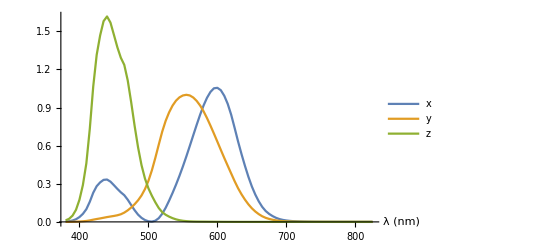

```mathematica
ListLinePlot[{{10^9*λ,x}ᵀ,{10^9*λ,y}ᵀ,{10^9*λ,z}ᵀ},PlotLegends->{"x","y","z"},AxesLabel->{"λ (nm)"}]
```

```mathematica
xtable=Table[{λ[[i]],x[[i]]},{i,1,Length[λ]}];
ytable=Table[{λ[[i]],y[[i]]},{i,1,Length[λ]}];
ztable=Table[{λ[[i]],z[[i]]},{i,1,Length[λ]}];
```

```mathematica
xbar=Interpolation[xtable];
ybar=Interpolation[ytable];
zbar=Interpolation[ztable];
```

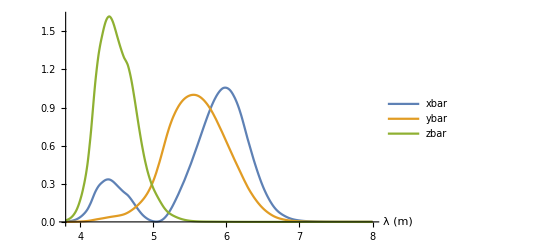

```mathematica
Plot[{xbar[λ],ybar[λ],zbar[λ]},{λ,380*10^-9,800*10^-9},PlotLegends->{"xbar","ybar","zbar"},AxesLabel->{"λ (m)"}]
```

```mathematica
(* frequency associated to a prime number *)
f[b_,p_]:=f0*Log[b,p]
```

```mathematica
(* perform convolution of power spectrum with color matching functions to obtain XYZ color values *)
XYZ[n_]:=Module[{fac=FactorInteger[n],X,Y,Z},
X=k*Sum[fac[[i,2]]*xbar[ c/f[base,fac[[i,1]]] ],{i,1,Length[fac]}];
Y=k*Sum[fac[[i,2]]*ybar[c/f[base,fac[[i,1]]] ],{i,1,Length[fac]}];
Z=k*Sum[fac[[i,2]]*zbar[c/f[base,fac[[i,1]]] ],{i,1,Length[fac]}];
Return[{X,Y,Z}]
]
```

```mathematica
(* assigns a color to a number in a natural way *)
Color[n_]:=ColorConvert[XYZColor@@XYZ[n],"RGB"]
```

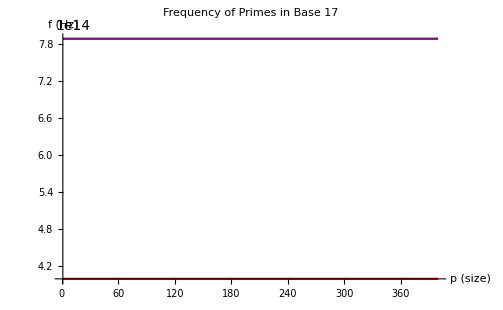

```mathematica
(* generate plot of freq. of each prime for a given base. include visibile range. *)
Plot[{f[p],fRED,fVIOLET},{p,1,400},PlotStyle->{Black,Red,Purple},AxesLabel->{"p (size)","f (Hz)"},PlotLabel->"Frequency of Primes in Base " <> ToString[base]]
```

```mathematica
(* Find the range of available primes/keys*)
pLow=Floor[Exp[Log[base]*fRED/f0]];
pHigh=Floor[Exp[Log[base]*fVIOLET/f0]];
primesInRange={};
Table[If[PrimeQ[n],AppendTo[primesInRange,n]],{n,pLow,pHigh}];
```

```mathematica
primesInRange
```

{17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263}

```mathematica
primeFreqs=Table[N[f[base,primesInRange[[i]]]],{i,1,Length[primesInRange]}]
```

{3.99733×10^14,4.15426×10^14,4.42382×10^14,4.75086×10^14,4.84496×10^14,5.09458×10^14,5.23942×10^14,5.30661×10^14,5.43211×10^14,5.60162×10^14,5.75293×10^14,5.79996×10^14,5.93233×10^14,6.01414×10^14,6.05334×10^14,6.16478×10^14,6.23447×10^14,6.33294×10^14,6.45438×10^14,6.5114×10^14,6.53906×10^14,6.59282×10^14,6.61894×10^14,6.66979×10^14,6.83458×10^14,6.87833×10^14,6.94152×10^14,6.96197×10^14,7.05998×10^14,7.0788×10^14,7.13377×10^14,7.18669×10^14,7.22089×10^14,7.27069×10^14,7.3188×10^14,7.33447×10^14,7.41034×10^14,7.42504×10^14,7.45398×10^14,7.46824×10^14,7.55085×10^14,7.62889×10^14,7.65397×10^14,7.66635×10^14,7.69078×10^14,7.72665×10^14,7.73841×10^14,7.79577×10^14,7.8291×10^14,7.86166×10^14}

```mathematica
Table[Style[primesInRange[[i]],Color[primesInRange[[i]]]],{i,1,Length[primesInRange]}]
```

{17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263}